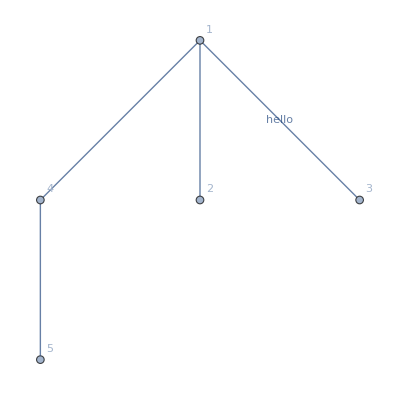

```mathematica
Graph[{1<->4,2<->1, 4 <-> 5,Labeled[3<->1,"hello"]},VertexLabels->"Name"];
HighlightGraph
```

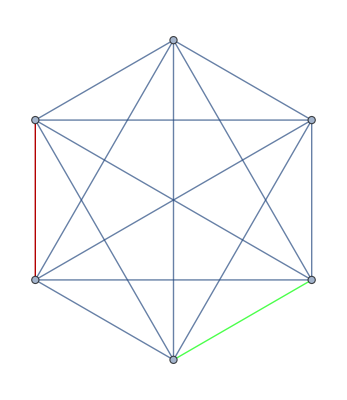

```mathematica
Das
HighlightGraph[CompleteGraph[6],{1<->2,Style[3<->4,Green]}]
```

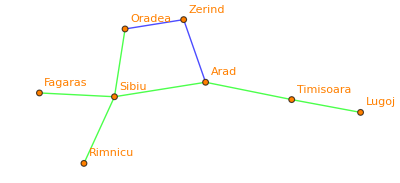

```mathematica
Print[Graph[Reverse[{1<->2,1<->3,2<->4,4<->3,4<->5,3<->6,3<-> 7,5<->"Lugoj"}],VertexLabels->{1->"Oradea",2->"Zerind",3->"Sibiu",4->"Arad",5->"Timisoara",6->"Fagaras",7->"Rimnicu","Lugoj"->"Lugoj"},VertexStyle->{Orange},EdgeStyle->{Green,1<->2->Blue,2<->4->Blue}]];
```

```mathematica
Oradea = {1, 380};
Zerind = {2, 374};
Arad = {3, 366};
Timisoara = {4, 329};
Lugoj = {5, 244};
Mehadia = {6, 241};
Drobeta = {7, 242};
Craiova = {8, 160};
Pitesti = {9, 100};
RumnicuVilcea = {10, 193};
Sibiu = {11, 253};
Fagaras = {12, 176};
Bucharest = {13, 0};
Giurgiu = {14, 77};
Urziceni = {15, 80};
Hirsona = {16, 151};
Eforie = {17, 161};
Vaslui = {18, 199};
Iasi = {19, 226};
Neamt = {20, 234};
Route = {
{Oradea, {Zerind, Sibiu}},
{Zerind, {Oradea, Arad}},
{Arad, {Zerind, Sibiu, Timisoara}},
{Timisoara, {Arad, Lugoj}},
{Lugoj, {Timisoara, Mehadia}},
{Mehadia, {Lugoj, Drobeta}},
{Drobeta, {Mehadia, Craiova}},
{Craiova, {Drobeta, RumnicuVilcea, Pitesti}},
{Pitesti, {Craiova, RumnicuVilcea, Bucharest}},
{RumnicuVilcea, {Craiova, Pitesti, Sibiu}},
{Sibiu, {Oradea, Arad, RumnicuVilcea, Fagaras}},
{Fagaras, {Sibiu, Bucharest}},
{Bucharest, {Giurgiu, Urziceni}},
{Giurgiu, {Bucharest}},
{Urziceni, {Bucharest, Hirsona, Vaslui}},
{Hirsona, {Urziceni, Eforie}},
{Eforie, {Hirsona}},
{Vaslui, {Urziceni, Iasi}},
{Iasi, {Vaslui, Neamt}},
{Neamt, {Iasi}}
};


functionDrawGraph::usage = "Retorna un grafo específico";
functionDrawGraph[] := Block[{},
(*Returns an specific graph*)
Return[Graph[{1 <-> 2, 2 <-> 3,  1 <-> 11,3 <->  4, 3 <-> 11, 4 <-> 5, 5 <-> 6, 6 <-> 7, 7 <-> 8, 8 <-> 10, 8 <-> 9, 9 <-> 10, 10 <-> 11, 11 <-> 12, 12 <-> 13, 13 <-> 14, 13 <-> 15, 9 <-> 13, 15 <-> 16, 15 <-> 18, 16 <-> 17, 18 <-> 19, 19 <-> 20}, VertexLabels -> {1 -> "Oradea", 2-> "Zerind", 11 -> "Sibiu", 3-> "Arad", 4 -> "Timisoara", 5 -> "Lugoj", 6 -> "Mehadia", 7-> "Drobera", 8 -> "Craiova", 9-> "Pitesti", 10 -> "Rimnicu Vilcea", 11 -> "Sibiu", 12 -> "Fagaras", 13 -> "Bucharest", 14 -> "Giurgiu", 15 -> "Urziceni", 16 -> "Hirsova", 17 -> "Eforie", 18 -> "Vaslui", 19 -> "Iasi", 20 -> "Neamt"}, EdgeLabels->{1 <-> 2 -> 71, 2 <-> 3 -> 75, 3<-> 11 -> 140, 1 <-> 11 -> 151, 4 <-> 5 -> 111, 3 <-> 4 -> 118, 5 <-> 6 -> 70, 6 <-> 7 -> 75, 7 <-> 8 -> 120, 8 <-> 9 -> 138, 8 <-> 10 -> 146, 9 <-> 10 -> 97, 10 <-> 11 -> 80, 11 <-> 12 -> 99, 12 <-> 13 -> 211, 9 <-> 13 -> 101, 13 <-> 14 -> 90, 13 <-> 15 -> 85, 15 <->16 -> 98, 16 <-> 17 -> 86, 15 <-> 18 -> 142, 18 <-> 19 -> 92, 19 <-> 20 -> 87}, ImageSize->1250]]
];
functionAEstrella[start_, end_] := Block[{inicio, fin, aux, current, i},
Print["Algoritmo A-estrella"];
inicio = start;
fin= end;
aux = {};
current = {};
i = 0;
For[i =1, i≤ Length[Route], i++,
current = Part[Route, i];
If[inicio == Part[current, 1],
Print["aqui anda"],
Print["nel pastel"]
]
]
];
functionAEstrella[1,2]
```

Algoritmo A-estrella